```mathematica
With[{stocka="NASDAQ:MSFT",stockb="NASDAQ:MSFT",n=10},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[First,Last],p]].Normalize[Map[Composition[Last,Last],p]]]},{p,part}]},
dot
]]]]]]]
```

{{Thu 13 Mar 1986 00:00:00GMT-8.,1.},{Fri 14 Mar 1986 00:00:00GMT-8.,1.},{Mon 17 Mar 1986 00:00:00GMT-8.,1.},{Tue 18 Mar 1986 00:00:00GMT-8.,1.},{Wed 19 Mar 1986 00:00:00GMT-8.,1.},{Thu 20 Mar 1986 00:00:00GMT-8.,1.},{Fri 21 Mar 1986 00:00:00GMT-8.,1.},{Mon 24 Mar 1986 00:00:00GMT-8.,1.},8493,{Mon 2 Dec 2019 00:00:00GMT-8.,1.},{Tue 3 Dec 2019 00:00:00GMT-8.,1.},{Wed 4 Dec 2019 00:00:00GMT-8.,1.},{Thu 5 Dec 2019 00:00:00GMT-8.,1.},{Fri 6 Dec 2019 00:00:00GMT-8.,1.},{Mon 9 Dec 2019 00:00:00GMT-8.,1.},{Tue 10 Dec 2019 00:00:00GMT-8.,1.}}
 |  |  |  |

```mathematica
With[{stocka="NASDAQ:MSFT",stockb="NASDAQ:MSFT",n=10},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
cleaned
]]]]]
```

{{Thu 13 Mar 1986 00:00:00GMT-8.,{1.03491,1.03491}},{Fri 14 Mar 1986 00:00:00GMT-8.,{1.01786,1.01786}},{Mon 17 Mar 1986 00:00:00GMT-8.,{0.974663,0.974663}},{Tue 18 Mar 1986 00:00:00GMT-8.,{0.981992,0.981992}},{Wed 19 Mar 1986 00:00:00GMT-8.,{0.973527,0.973527}},8508,{Wed 18 Dec 2019 00:00:00GMT-8.,{1.00868,1.00868}},{Thu 19 Dec 2019 00:00:00GMT-8.,{1.01092,1.01092}},{Fri 20 Dec 2019 00:00:00GMT-8.,{1.,1.}},{Mon 23 Dec 2019 00:00:00GMT-8.,{0.999809,0.999809}}}
 |  |  |  |

```mathematica
With[{stocka="NASDAQ:MSFT",stockb="NASDAQ:MSFT",n=10},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[First,Last],p]].Normalize[Map[Composition[Last,Last],p]]]},{p,part}]},
dot
]]]]]]]
```

{{Thu 13 Mar 1986 00:00:00GMT-8.,1.},{Fri 14 Mar 1986 00:00:00GMT-8.,1.},{Mon 17 Mar 1986 00:00:00GMT-8.,1.},{Tue 18 Mar 1986 00:00:00GMT-8.,1.},{Wed 19 Mar 1986 00:00:00GMT-8.,1.},{Thu 20 Mar 1986 00:00:00GMT-8.,1.},{Fri 21 Mar 1986 00:00:00GMT-8.,1.},{Mon 24 Mar 1986 00:00:00GMT-8.,1.},8493,{Mon 2 Dec 2019 00:00:00GMT-8.,1.},{Tue 3 Dec 2019 00:00:00GMT-8.,1.},{Wed 4 Dec 2019 00:00:00GMT-8.,1.},{Thu 5 Dec 2019 00:00:00GMT-8.,1.},{Fri 6 Dec 2019 00:00:00GMT-8.,1.},{Mon 9 Dec 2019 00:00:00GMT-8.,1.},{Tue 10 Dec 2019 00:00:00GMT-8.,1.}}
 |  |  |  |

```mathematica
With[{stocka="NASDAQ:MSFT",stockb="NASDAQ:AMZN",n=10},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[First,Last],p]].Normalize[Map[Composition[Last,Last],p]]]},{p,part}]},
dot
]]]]]]]
```

{{Thu 15 May 1997 00:00:00GMT-8.,0.998356},{Fri 16 May 1997 00:00:00GMT-8.,0.998624},{Mon 19 May 1997 00:00:00GMT-8.,0.998592},{Tue 20 May 1997 00:00:00GMT-8.,0.998776},{Wed 21 May 1997 00:00:00GMT-8.,0.999431},{Thu 22 May 1997 00:00:00GMT-8.,0.999452},{Fri 23 May 1997 00:00:00GMT-8.,0.999531},5669,{Tue 3 Dec 2019 00:00:00GMT-8.,0.99997},{Wed 4 Dec 2019 00:00:00GMT-8.,0.999972},{Thu 5 Dec 2019 00:00:00GMT-8.,0.999977},{Fri 6 Dec 2019 00:00:00GMT-8.,0.99997},{Mon 9 Dec 2019 00:00:00GMT-8.,0.999969},{Tue 10 Dec 2019 00:00:00GMT-8.,0.99997}}
 |  |  |  |

```mathematica
DateListPlot[
Out[4]
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
]
```

-Graphics-

```mathematica
Histogram[
Map[Last,Out[4]]
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
Permutations[Range@3]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

```mathematica
Permutations[Range@3,{2}]
```

{{1,2},{1,3},{2,1},{2,3},{3,1},{3,2}}

```mathematica
Subsets[Range@3,{2}]
```

{{1,2},{1,3},{2,3}}

```mathematica
{"NASDAQ:AAPL"
```

```mathematica
With[{stocka="NASDAQ:MSFT",stockb="NASDAQ:AMZN",n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[First,Last],p]].Normalize[Map[Composition[Last,Last],p]]]},{p,part}]},
dot
]]]]]]]
```

{{Thu 15 May 1997 00:00:00GMT-8.,0.998679},{Fri 16 May 1997 00:00:00GMT-8.,0.997751},{Mon 19 May 1997 00:00:00GMT-8.,0.9975},{Tue 20 May 1997 00:00:00GMT-8.,0.99777},{Wed 21 May 1997 00:00:00GMT-8.,0.999482},{Thu 22 May 1997 00:00:00GMT-8.,0.999566},{Fri 23 May 1997 00:00:00GMT-8.,0.999811},5674,{Tue 10 Dec 2019 00:00:00GMT-8.,0.999962},{Wed 11 Dec 2019 00:00:00GMT-8.,0.999961},{Thu 12 Dec 2019 00:00:00GMT-8.,0.999961},{Fri 13 Dec 2019 00:00:00GMT-8.,0.999948},{Mon 16 Dec 2019 00:00:00GMT-8.,0.999946},{Tue 17 Dec 2019 00:00:00GMT-8.,0.999983}}
 |  |  |  |

```mathematica
DateListPlot[
Out[12]
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
]
```

-Graphics-

```mathematica
Histogram[
Map[Last,Out[12]]
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
```

-Graphics-

```mathematica
EntityClass["Financial",{EntityProperty["Financial","EntityClasses"]->EntityClass["Financial","InformationTechnologyServices"],EntityProperty["Financial","MarketCap"]->TakeLargest[5]}]
```

EntityClass[Financial,{entity classes→Information Technology Services,market capitalization→TakeLargest[5]}]

```mathematica
EntityList@EntityClass["Financial",{EntityProperty["Financial","EntityClasses"]->EntityClass["Financial","InformationTechnologyServices"],EntityProperty["Financial","MarketCap"]->TakeLargest[5]}]
```

{Atlassian Corporation PLC,Rackspace Hosting,IGate,Sapient,Syntel}

```mathematica
EntityList@EntityClass["Financial",{EntityProperty["Financial","Exchange"]->"Nasdaq",EntityProperty["Financial","MarketCap"]->TakeLargest[5]}]
```

Missing[QueryValueIncompatibleWithProperty,{Financial,Exchange,Nasdaq}]

```mathematica
EntityList@EntityClass["Financial",{EntityProperty["Financial","Exchange"]->"Nasdaq",EntityProperty["Financial","MarketCap"]->TakeLargest[5]}]
```

Missing[QueryValueIncompatibleWithProperty,{Financial,Exchange,Nasdaq}]

```mathematica
FinancialData["NASDAQ:GOOG","Exchange"]
```

Nasdaq

```mathematica
EntityList@EntityClass["Financial",{EntityProperty["Financial","Exchange"]->EqualTo@"Nasdaq",EntityProperty["Financial","MarketCap"]->TakeLargest[5]}]
```

Missing[QueryValueIncompatibleWithProperty,{Financial,Exchange,EqualTo[Nasdaq]}]

```mathematica
DateListPlot[
With[{stocka="NASDAQ:MSFT",stockb="NASDAQ:AMZN",n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Differences@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Differences@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[First,Last],p]].Normalize[Map[Composition[Last,Last],p]]]},{p,part}]},
dot
]]]]]]]
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
]
```

-Graphics-

```mathematica
{"AAPL","MSFT","AMZN","INTC","FB","WORK","CLDR","CSCO","AMD","NVIDIA","UBER","LYFT"}
```

{AAPL,MSFT,AMZN,INTC,FB,WORK,CLDR,CSCO,AMD,NVIDIA,UBER,LYFT}

```mathematica
Map[StringJoin["NASDAQ:",#]&,Out[23]]
```

{NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:AMZN,NASDAQ:INTC,NASDAQ:FB,NASDAQ:WORK,NASDAQ:CLDR,NASDAQ:CSCO,NASDAQ:AMD,NASDAQ:NVIDIA,NASDAQ:UBER,NASDAQ:LYFT}

```mathematica
Table[FinancialData[f,"Close",All],{f,Map[StringJoin["NASDAQ:",#]&,Out[23]]}]
```

FinancialData::notent: NASDAQ:WORK is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: NASDAQ:CLDR is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

FinancialData::notent: NASDAQ:NVIDIA is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

General::stop: Further output of FinancialData::notent will be suppressed during this calculation.

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],Missing[NotAvailable],Missing[NotAvailable],TimeSeries[…],TimeSeries[…],Missing[NotAvailable],Missing[NotAvailable],TimeSeries[…]}

```mathematica
{"AAPL","MSFT","AMZN","INTC","FB","CSCO","AMD","UBER","LYFT"}
```

{AAPL,MSFT,AMZN,INTC,FB,CSCO,AMD,UBER,LYFT}

```mathematica
Map[StringJoin["NASDAQ:",#]&,Out[26]]
```

{NASDAQ:AAPL,NASDAQ:MSFT,NASDAQ:AMZN,NASDAQ:INTC,NASDAQ:FB,NASDAQ:CSCO,NASDAQ:AMD,NASDAQ:UBER,NASDAQ:LYFT}

```mathematica
Table[FinancialData[f,"Close",All],{f,Map[StringJoin["NASDAQ:",#]&,Out[26]]}]
```

FinancialData::notent: NASDAQ:UBER is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

{TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],TimeSeries[…],Missing[NotAvailable],TimeSeries[…]}

```mathematica
ParallelTable[
With[{stocka="NASDAQ:MSFT",stockb="NASDAQ:AMZN",n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[First,Last],p]].Normalize[Map[Composition[Last,Last],p]]]},{p,part}]},
{DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
],
Histogram[
Map[Last,dot]
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
}
]]]]]]]
,{stocks,Subsets[{"NASDAQ:GOOGL","NASDAQ:AMZN","NASDAQ:MSFT","NASDAQ:AAPL"},{2}]}]
```

Initializing FinancialData indices ....

Initializing FinancialData indices ....

Initializing FinancialData indices ....

«5 more identical outputs»

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Grid@
ParallelTable[
With[{stocka=First@stocks,stockb=Last@stocks,n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[First,Last],p]].Normalize[Map[Composition[Last,Last],p]]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
}
]]]]]]]]
,{stocks,Subsets[{"NASDAQ:GOOGL","NASDAQ:AMZN","NASDAQ:MSFT","NASDAQ:AAPL"},{2}]}]
```

NASDAQ:GOOGL | NASDAQ:AMZN | 0.999798 | 0.999932 | -7.05932 | 64.5684 | -Graphics- | -Graphics-
NASDAQ:GOOGL | NASDAQ:MSFT | 0.999872 | 0.999949 | -6.70607 | 64.5354 | -Graphics- | -Graphics-
NASDAQ:GOOGL | NASDAQ:AAPL | 0.999835 | 0.999931 | -5.0565 | 39.7969 | -Graphics- | -Graphics-
NASDAQ:AMZN | NASDAQ:MSFT | 0.999521 | 0.999867 | -4.39043 | 28.1879 | -Graphics- | -Graphics-
NASDAQ:AMZN | NASDAQ:AAPL | 0.999392 | 0.999826 | -9.17017 | 153.493 | -Graphics- | -Graphics-
NASDAQ:MSFT | NASDAQ:AAPL | 0.999697 | 0.999855 | -21.982 | 676.082 | -Graphics- | -Graphics-

```mathematica
Grid@
ParallelTable[
With[{stocka=First@stocks,stockb=Last@stocks,n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[First,Last],p]].Normalize[Map[Composition[Last,Last],p]]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
}
]]]]]]]]
,{stocks,Subsets[{"NASDAQ:INTC","NASDAQ:AMZN","NASDAQ:AMD","NYSE:CHK"},{2}]}]
```

Grid[Join[$Failed,$Failed,$Failed,$Failed]]

```mathematica
Grid@
ParallelTable[
With[{stocka=First@stocks,stockb=Last@stocks,n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[First,Last],p]].Normalize[Map[Composition[Last,Last],p]]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
}
]]]]]]]]
,{stocks,Subsets[{"NASDAQ:INTC","NASDAQ:AMZN","NYSE:CHK"},{2}]}]
```

Grid[Join[HoldComplete[{{NASDAQ:INTC,NASDAQ:AMZN,0.999465,0.999838,-4.20459,26.2033,-Graphics-,-Graphics-}}],$Failed,$Failed]]

```mathematica
FinancialData["NYSE:CHK","Close"]
```

0.94 $

```mathematica
FinancialData["NYSE:CHK","Close",All]
```

TimeSeries[…]

```mathematica
Grid@
ParallelTable[
With[{stocka=First@stocks,stockb=Last@stocks,n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[First,Last],p]].Normalize[Map[Composition[Last,Last],p]]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
}
]]]]]]]]
,{stocks,Subsets[{"NYSE:IBM","NYSE:CHK"},{2}]}]
```

Join::normal: Nonatomic expression expected at position 1 in Join[$Failed].

Grid[Join[$Failed]]

```mathematica
With[{stocka="NYSE:IBM",stockb="NYSE:CHK",n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[First,Last],p]].Normalize[Map[Composition[Last,Last],p]]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
}
]]]]]]]]
```

{NYSE:IBM,NYSE:CHK,0.999311,0.999692,-4.27635,28.4039,-Graphics-,-Graphics-}

```mathematica
With[{stocka="NYSE:IBM",stockb="NYSE:CHK",n=5},
With[{tsa=FinancialData[stocka,"Price",All],tsb=FinancialData[stockb,"Price",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[First,Last],p]].Normalize[Map[Composition[Last,Last],p]]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
}
]]]]]]]]
```

{NYSE:IBM,NYSE:CHK,0.999311,0.999692,-4.27635,28.4039,-Graphics-,-Graphics-}

```mathematica
With[{stocka="NASDAQ:FB",stockb="NYSE:CHK",n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[First,Last],p]].Normalize[Map[Composition[Last,Last],p]]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
}
]]]]]]]]
```

{NASDAQ:FB,NYSE:CHK,0.9992,0.99961,-4.04111,24.2663,-Graphics-,-Graphics-}

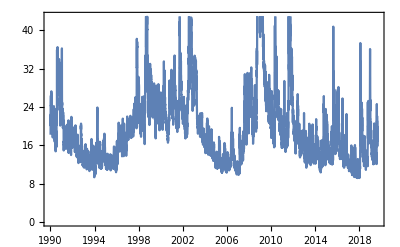

```mathematica
DateListPlot@FinancialData["^VIX","Price",All]
```

```mathematica
With[{stocka="^VIX",stockb="NASDAQ:FB",n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[First,Last],p]].Normalize[Map[Composition[Last,Last],p]]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
}
]]]]]]]]
```

{^VIX,NASDAQ:FB,0.996559,0.998189,-7.34291,85.1644,-Graphics-,-Graphics-}

```mathematica
With[{stocka="^VIX",stockb="NASDAQ:FB",n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[Sign,#-1&,First,Last],p]].Normalize[Map[Composition[Sign,#-1&,Last,Last],p]]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
}
]]]]]]]]
```

{^VIX,NASDAQ:FB,-0.3005,-0.2,0.306552,2.50925,-Graphics-,-Graphics-}

```mathematica
With[{stocka="^VIX",stockb="NASDAQ:FB",n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,Covariance[Map[Composition[Sign,#-1&,First,Last],p],Map[Composition[Sign,#-1&,Last,Last],p]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
}
]]]]]]]]
```

{^VIX,NASDAQ:FB,-954/3025,-2/5,3459329793/(4870463 √9740926),117391429901661/47442819668738,-Graphics-,-Graphics-}

```mathematica
Grid@
ParallelTable[
With[{stocka=First@stocks,stockb=Last@stocks,n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,Covariance[Map[Composition[Sign,#-1&,First,Last],p],Map[Composition[Sign,#-1&,Last,Last],p]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
}
]]]]]]]]
,{stocks,Subsets[{"NASDAQ:GOOGL","NASDAQ:AMZN","NASDAQ:MSFT","NASDAQ:AAPL"},{2}]}]
```

Grid[Join[HoldComplete[{{NASDAQ:GOOGL,NASDAQ:AMZN,15271/38600,2/5,-1384387486638/(357480779 √357480779),313901016066295877/127792507354446841,-Graphics-,-Graphics-},{NASDAQ:GOOGL,NASDAQ:MSFT,25101/77200,2/5,-16635874209258/(1591705619 √1591705619),955525364602183331/361932396793739023,-Graphics-,-Graphics-}}],$Failed,HoldComplete[{{NASDAQ:AMZN,NASDAQ:AAPL,633/2420,1/5,-(585896411 √(47/17028435))/5676145,997950964537889/386623464732300,-Graphics-,-Graphics-}}],HoldComplete[{{NASDAQ:MSFT,NASDAQ:AAPL,12998/42565,2/5,-(21768165677544 √(2/3589642097))/3589642097,64438380033057849101/25771060769109114818,-Graphics-,-Graphics-}}]]]

```mathematica
Grid@
ParallelTable[
With[{stocka=First@stocks,stockb=Last@stocks,n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,Covariance[Map[Composition[Sign,#-1&,First,Last],p],Map[Composition[Sign,#-1&,Last,Last],p]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
}
]]]]]]]]
,{stocks,Subsets[{"NYSE:CHK","NASDAQ:AMZN","NASDAQ:MSFT","NASDAQ:AAPL"},{2}]}]
```

Grid[Join[$Failed,$Failed,$Failed,$Failed]]

```mathematica
With[{stocka="^VIX",stockb="NASDAQ:FB",n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[Sign,#-1&,First,Last],p]].Normalize[Map[Composition[Sign,#-1&,Last,Last],p]]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Full
]
}
]]]]]]]]
```

{^VIX,NASDAQ:FB,-0.3005,-0.2,0.306552,2.50925,-Graphics-,-Graphics-}

```mathematica
With[{stocka="^VIX",stockb="NASDAQ:FB",n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[Sign,#-1&,First,Last],p]].Normalize[Map[Composition[Sign,#-1&,Last,Last],p]]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow"
]
}
]]]]]]]]
```

{^VIX,NASDAQ:FB,-0.3005,-0.2,0.306552,2.50925,-Graphics-,-Graphics-}

```mathematica
With[{stocka="^VIX",stockb="NASDAQ:FB",n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[Sign,#-1&,First,Last],p]].Normalize[Map[Composition[Sign,#-1&,Last,Last],p]]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large
]
}
]]]]]]]]
```

{^VIX,NASDAQ:FB,-0.3005,-0.2,0.306552,2.50925,-Graphics-,-Graphics-}

```mathematica
With[{stocka="^VIX",stockb="NASDAQ:FB",n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[Sign,#-1&,First,Last],p]].Normalize[Map[Composition[Sign,#-1&,Last,Last],p]]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large
]
}
]]]]]]]]
```

```mathematica
g[n_]:=Piecewise[{{1, n>1}, {0, n==1}, {-1, n<1}}]
```

```mathematica
With[{stocka="^VIX",stockb="NASDAQ:FB",n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize[Map[Composition[g,First,Last],p]].Normalize[Map[Composition[g,Last,Last],p]]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large
]
}
]]]]]]]]
```

{^VIX,NASDAQ:FB,-0.300869,-0.2,0.298915,2.49151,-Graphics-,-Graphics-}

```mathematica
With[{stocka="^VIX",stockb="NASDAQ:FB",n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,Covariance[Normalize[Map[Composition[g,First,Last],p]],Normalize[Map[Composition[g,Last,Last],p]]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large
]
}
]]]]]]]]
```

{^VIX,NASDAQ:FB,1/1815(-11/(2 √5)-(-3/(√5)-√5)/(5 √5)+(19 (1/(√5)-√5))/(2 √5)-(2 (-3/(√5)+√5))/(√5)-(39 (-1/(√5)+√5))/(4 √5)-(31 (3/(√5)+√5))/(20 √5)+1/20 (-1/(√5)+√5+1/2 (-1/(√5)-√5)+1/2 (1/(√5)-√5))+1/5 (1/2 (-1/(√5)-√5)+3/2 (1/(√5)-√5))+36+19/20 (-(2 (3/(√5)-√5))/(√5)-(3/(√5)+√5)/(√5))+49/10 ((2 (3/(√5)-√5))/(√5)-(3/(√5)+√5)/(√5))+19/10 ((4 (3/(√5)-√5))/(√5)-(3/(√5)+√5)/(√5))+1/20 (-(4 (3/(√5)-√5))/(√5)+(3/(√5)+√5)/(√5))+3/5 (-(2 (3/(√5)-√5))/(√5)+(3/(√5)+√5)/(√5))+37/20 ((2 (3/(√5)-√5))/(√5)+(3/(√5)+√5)/(√5))+13/20 ((4 (3/(√5)-√5))/(√5)+(3/(√5)+√5)/(√5))),1/20 (-(1/(√5)-√5)/(√5)-(2 (1/(√5)+√5))/(√5)),(11 √15 ((19 1)/1195803675+74))/(1)^(3/2),(1815 ((19 (11/1+69)^4)/2170383670125+11 (-1/1+1)^4+(1)^4+69+12 1^4+37 (1)^4+13 (1/20 (411/(√5)+1)+1)^4))/(((19 (1)^2)/658845+11 (1)^2+71+37 1^2+13 (1+1)^2)^2),-Graphics-,-Graphics-}
 |  |  |  |

```mathematica
With[{stocka="^VIX",stockb="NASDAQ:FB",n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,Covariance[Normalize[Map[Composition[g,First,Last],p]],Normalize[Map[Composition[g,Last,Last],p]]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,N@Mean[data],N@Median[data],N@Skewness[data],N@Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large
]
}
]]]]]]]]
```

{^VIX,NASDAQ:FB,-0.0634433,-0.08,0.219672,2.4497,-Graphics-,-Graphics-}

```mathematica
With[{stocka="^VIX",stockb="NASDAQ:FB",n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,Covariance[Map[Composition[g,First,Last],p],Map[Composition[g,Last,Last],p]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,N@Mean[data],N@Median[data],N@Skewness[data],N@Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large
]
}
]]]]]]]]
```

{^VIX,NASDAQ:FB,-0.316033,-0.4,0.213267,2.43989,-Graphics-,-Graphics-}

```mathematica
Grid@
ParallelTable[
With[{stocka=First@stocks,stockb=Last@stocks,n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize@Map[Composition[g,First,Last],p].Normalize@Map[Composition[g,Last,Last],p]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large
]
}
]]]]]]]]
,{stocks,Subsets[{"NYSE:CHK","NASDAQ:AMZN","NASDAQ:MSFT","NASDAQ:AAPL"},{2}]}]
```

Parallel`Developer`QueueRun::hmm: Received unexpected result Null from KernelObject[4,local].

Parallel`Developer`QueueRun::hmm: Received unexpected result Null from KernelObject[3,local].

Parallel`Developer`QueueRun::hmm: Received unexpected result Null from KernelObject[2,local].

General::stop: Further output of Parallel`Developer`QueueRun::hmm will be suppressed during this calculation.

$Aborted

```mathematica
Grid@
Table[
With[{stocka=First@stocks,stockb=Last@stocks,n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize@Map[Composition[g,First,Last],p].Normalize@Map[Composition[g,Last,Last],p]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large
]
}
]]]]]]]]
,{stocks,Subsets[{"NYSE:CHK","NASDAQ:AMZN","NASDAQ:AAPL"},{2}]}]
```

NYSE:CHK | NASDAQ:AMZN | 0.130826 | 0.2 | -0.0614549 | 2.53108 | -Graphics- | -Graphics-
NYSE:CHK | NASDAQ:AAPL | 0.12284 | 0.2 | -0.125777 | 2.53029 | -Graphics- | -Graphics-
NASDAQ:AMZN | NASDAQ:AAPL | 0.260154 | 0.2 | -0.265489 | 2.66442 | -Graphics- | -Graphics-

```mathematica
Binomial[3,2]
```

3

```mathematica
Grid@
Table[
With[{stocka=First@stocks,stockb=Last@stocks,n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize@Map[Composition[First,Last],p].Normalize@Map[Composition[Last,Last],p]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large
]
}
]]]]]]]]
,{stocks,Subsets[{"NYSE:CHK","NASDAQ:AMZN","NASDAQ:AAPL"},{2}]}]
```

NYSE:CHK | NASDAQ:AMZN | 0.999004 | 0.999606 | -3.51909 | 20.1607 | -Graphics- | -Graphics-
NYSE:CHK | NASDAQ:AAPL | 0.999136 | 0.999602 | -10.1864 | 195.496 | -Graphics- | -Graphics-
NASDAQ:AMZN | NASDAQ:AAPL | 0.999392 | 0.999826 | -9.17017 | 153.493 | -Graphics- | -Graphics-

```mathematica
Grid@
Table[
With[{stocka=First@stocks,stockb=Last@stocks,n=5},
With[{tsa=FinancialData[stocka,"Close",All],tsb=FinancialData[stockb,"Close",All]},
With[{tra=Transpose[{tsa["Dates"][[;;-2]],Ratios@tsa["Values"]}],trb=Transpose[{tsb["Dates"][[;;-2]],Ratios@tsb["Values"]}]},
With[{filt=Select[GatherBy[Join[tra,trb],First],Length@#==2&]},
With[{cleaned=Table[{First@First@f,{Last@First@f,Last@Last@f}},{f,filt}]},
With[{part=Partition[cleaned,n,1]},
With[{dot=Table[{First@First@p,N[Normalize@Map[Composition[g,First,Last],p].Normalize@Map[Composition[g,Last,Last],p]]},{p,part}]},
With[{data=Map[Last,dot]},
{stocka,stockb,Mean[data],Median[data],Skewness[data],Kurtosis[data],DateListPlot[
dot
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large,Joined->False
],
Histogram[
data
,PlotRange->Full,PlotTheme->"Marketing",ColorFunction->"DarkRainbow",AspectRatio->1/3,ImageSize->Large
]
}
]]]]]]]]
,{stocks,Subsets[{"NYSE:CHK","NASDAQ:AMZN","NASDAQ:AAPL","NYSE:IBM","NASDAQ:FB"},{2}]}]
```

NYSE:CHK | NASDAQ:AMZN | 0.130826 | 0.2 | -0.0614549 | 2.53108 | -Graphics- | -Graphics-
NYSE:CHK | NASDAQ:AAPL | 0.12284 | 0.2 | -0.125777 | 2.53029 | -Graphics- | -Graphics-
NYSE:CHK | NYSE:IBM | 0.135797 | 0.2 | -0.139872 | 2.55913 | -Graphics- | -Graphics-
NYSE:CHK | NASDAQ:FB | 0.113294 | 0.2 | -0.0667199 | 2.55079 | -Graphics- | -Graphics-
NASDAQ:AMZN | NASDAQ:AAPL | 0.260154 | 0.2 | -0.265489 | 2.66442 | -Graphics- | -Graphics-
NASDAQ:AMZN | NYSE:IBM | 0.259309 | 0.2 | -0.272971 | 2.68748 | -Graphics- | -Graphics-
NASDAQ:AMZN | NASDAQ:FB | 0.391164 | 0.6 | -0.336169 | 2.65854 | -Graphics- | -Graphics-
NASDAQ:AAPL | NYSE:IBM | 0.272304 | 0.2 | -0.303918 | 2.62769 | -Graphics- | -Graphics-
NASDAQ:AAPL | NASDAQ:FB | 0.266526 | 0.2 | -0.294898 | 2.59539 | -Graphics- | -Graphics-
NYSE:IBM | NASDAQ:FB | 0.182107 | 0.2 | -0.202435 | 2.67006 | -Graphics- | -Graphics-